```mathematica
ClearAll["Global`*"];
```

## Dose-response simulations

## Dose-response functions

Here are the defined the (individual) dose-response functions of a compound on a given parameter:

The idea here is to investigate the impact of a pesticide on a predator-prey ecosystem, with the method developed in `method_jacob.nb`.

```mathematica
ClearAll[DRLogRNFun,DRFunLog,DRFunLogExp];

(*Equivalent to DR_logRN_fun*)
DRLogRNFun[Dose_,Rmin_,Rmax_,beta_,NEC_]:=Module[{logyhat,yhat},logyhat=Rmin+(Rmax-Rmin)*Exp[-Exp[beta]*(Dose-NEC)*Boole[Dose>NEC]];
yhat=Exp[logyhat];
yhat]

(*Equivalent to DR_fun_log*)
DRFunLog[Dose_,alpha_,beta_,NEC_]:=Piecewise[{{Log[alpha],Dose<NEC},{Log[alpha]-Exp[beta]*(Dose-NEC),Dose>=NEC}}]

(*Equivalent to DR_fun_log_exp*)
DRFunLogExp[Dose_,alpha_,beta_,NEC_]:=Exp[DRFunLog[Dose,alpha,beta,NEC]]
```

## Dose-response simulations

We will firstly generate a population of 10000 individuals, each with a phenotypic trait x following a normal distribution around , with standard deviation σ.
Each individual also has a different minimal pesticide concentration (NEC: No Effect Concentration) above which the trait x decays to zero.
For a single individual, the dose-response function is:

Here, we’ll take , , , , and , with  and Σ=(σ | 0
0 | σ_NEC)(1 | ρ_(x_0,NEC)
ρ_(x_0,NEC) | 1)(σ | 0
0 | σ_NEC).
Remark: one could also consider an individual variation of β, but in practice, this is difficult to measure, as one individual can only be used once for measurement (destructive measurements).

```mathematica
(* --- GLOBAL PARAMETERS --- *)
x0=100;
beta=-3.5;
Dose=Range[0,100,1];
NEC=25;
nID=10000;
CVx=0.2;
CVnec=0.2;
sigma=0.08;
```

Here is the individual dose-response function:

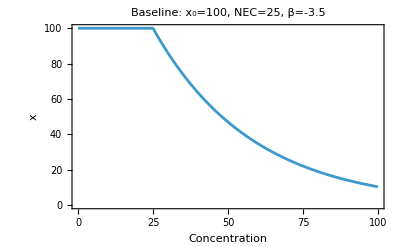

```mathematica
Manipulate[
Plot[DRFunLogExp[d,X0,β,nec],{d,0,100}],
{{X0,x0},10, 200},{{β,beta},-10,-1},{{nec,NEC},5,80},
FrameLabel->{"Concentration","x"}
]
(*Check the baseline deterministic dose–response function*)
baseline=Table[
{d,DRFunLogExp[d,x0,beta,NEC]},
{d,Dose}
];
plotBaseline[baseline_]:=ListLinePlot[
baseline,
PlotLabel->StringForm["Baseline: x_0=``, NEC=``, β=``",x0,NEC,beta],
Frame->{{True,False},{True,False}},
FrameLabel->{"Concentration","x"}]
baselinePlot=plotBaseline[baseline];
baselinePlot
```

Let’s first generate all 10000 individuals, one set with positive correlation between x and NEC, another with negative correlation, and a last one with no correlation:

```mathematica
GenerateIndividuals[x0_,NEC_,CVx_,CVnec_,rhoX0NEC_,nID_]:=Module[{Mu,sigmas,rhoMat,Sigma,dist,samples},
Mu={x0,NEC};
sigmas={x0*CVx,NEC*CVnec};
rhoMat={{1,rhoX0NEC},{rhoX0NEC,1}};
Sigma=DiagonalMatrix[sigmas].rhoMat.DiagonalMatrix[sigmas];
dist=MultinormalDistribution[Mu,Sigma];
samples=RandomVariate[dist,nID];
Table[
<|"x0"->samples[[i,1]],
"NEC"->samples[[i,2]],
"ID"->i|>,
{i,nID}
]
]
SeedRandom[42];
rhoX0NEC=0.9;
individualsPos=GenerateIndividuals[x0,NEC,CVx,CVnec,rhoX0NEC,nID];
individualsNeg=GenerateIndividuals[x0,NEC,CVx,CVnec,-rhoX0NEC,nID];
individualsNull=GenerateIndividuals[x0,NEC,CVx,CVnec,0,nID];
```

Here are the three populations distributions:

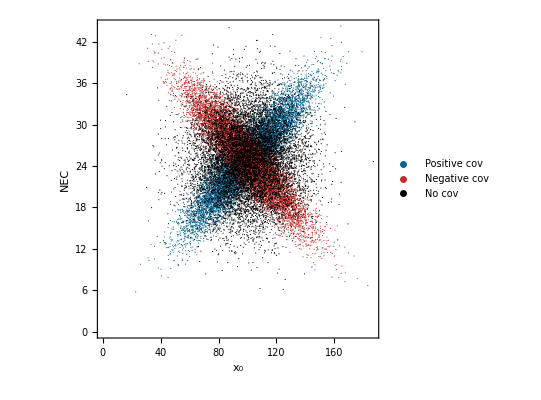

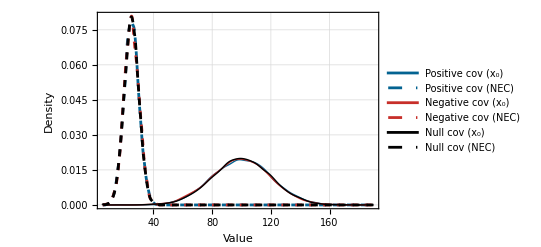

```mathematica
colPos=RGBColor[0.01,0.39,0.57];
colNeg=RGBColor[0.78,0.18,0.16];
plotDistrib[individualsPos_,individualsNeg_,individualsNull_,colPos_,colNeg_]:=Module[{dataPos,dataNeg,dataNull,listPlot,histogram},
dataPos=individualsPos[[All,{"x0","NEC"}]]/.assoc_Association:>{assoc["x0"], assoc["NEC"]};
dataNeg=individualsNeg[[All,{"x0","NEC"}]]/.assoc_Association:>{assoc["x0"],assoc["NEC"]};
dataNull=individualsNull[[All,{"x0","NEC"}]]/.assoc_Association:>{assoc["x0"],assoc["NEC"]};
listPlot=ListPlot[
{dataPos,dataNeg,dataNull},
PlotStyle->{
Directive[colPos,PointSize[0.002]],(*blue tone*)
Directive[colNeg,PointSize[0.002]],(*red tone*)
Directive[Black,PointSize[0.002]]
},
Frame->True,FrameLabel->{"x_0","NEC"},Axes->False,AspectRatio->1,PlotLegends->{"Positive cov","Negative cov", "No cov"}
];
histogram=SmoothHistogram[
{individualsPos[[All,"x0"]],individualsPos[[All,"NEC"]],individualsNeg[[All,"x0"]],individualsNeg[[All,"NEC"]],individualsNull[[All,"x0"]],individualsNull[[All,"NEC"]]},
PlotLegends->{"Positive cov (x_0)", "Positive cov (NEC)", "Negative cov (x_0)", "Negative cov (NEC)", "Null cov (x_0)", "Null cov (NEC)"},
PlotRange->All,
FrameLabel->{"Value","Density"},
PlotTheme->"Detailed",
PlotStyle->{
Directive[colPos,Thick],
Directive[colPos,Dashed],
Directive[colNeg,Thick],
Directive[colNeg,Dashed],
Directive[Black,Thick],
Directive[Black,Dashed]
}
];
{listPlot,histogram}
]
{listPlot,histogram}=plotDistrib[individualsPos,individualsNeg,individualsNull,colPos,colNeg];
listPlot
histogram
```

We can now compute the population distribution for each dose, and plot mean  and standard deviation σ for varying concentrations (this takes a few moments):

```mathematica
ClearAll[SimulateDoseResponse];
SimulateDoseResponse[individuals_List]:=Module[{records,data},
records=Flatten[
Table[
With[{x0=ind["x0"],b=beta,n=ind["NEC"]},
Table[
Module[{logyhat,yhat,y},
logyhat=DRFunLog[d,x0,b,n];
yhat=Exp[logyhat];
y=RandomVariate[LogNormalDistribution[logyhat,sigma]];
<|"ID"->ind["ID"],"Dose"->d,"logyhat"->logyhat,"yhat"->yhat,"y"->y|>],{d,Dose}
]
],{ind,individuals}]
,1
];
data=GroupBy[records,#Dose&];
(*Compute mean and sd per Dose*)
Table[
With[{vals=data[d]},
<|"Dose"->d,"yhatMean"->Mean[vals[[All,"yhat"]]],"yhatSD"->StandardDeviation[vals[[All,"yhat"]]]|>
],{d,Keys[data]}
]
];
(*Positive covariance between alpha and NEC*)
summaryPos=SimulateDoseResponse[individualsPos];
(*Negative covariance between alpha and NEC*)
summaryNeg=SimulateDoseResponse[individualsNeg];
(*No correlation between alpha and NEC*)
summaryNull=SimulateDoseResponse[individualsNull];
(*Concentration, mean Table for each population*)
meanPos=summaryPos[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
meanNeg=summaryNeg[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
meanNull=summaryNull[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
(*Concentration, standard deviation for each population*)
stdPos=summaryPos[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
stdNeg=summaryNeg[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
stdNull=summaryNull[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
```

Let’s plot the resulting population response to different concentrations:

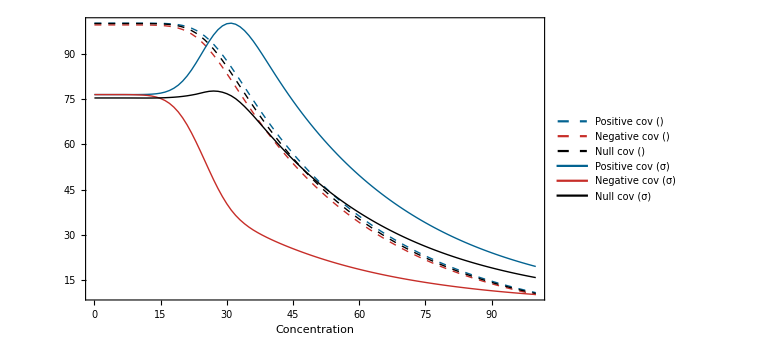

```mathematica
plotResponse[meanPos_,meanNeg_,meanNull_,stdPos_,stdNeg_,stdNull_,majorStep_,colPos_,colNeg_]:=Module[
{meanMin,meanMax,stdMin,stdMax,a,b,mapStd,invMap,majorTicks,minorTicks,rightTicks,frameTicks,plotMean,plotStd,dualPlot,dualPlotLegend},
(*Visual parameters*)
meanMin=Min[Flatten[{meanPos[[All,2]],meanNeg[[All,2]],meanNull[[All,2]]}]];
meanMax=Max[Flatten[{meanPos[[All,2]],meanNeg[[All,2]],meanNull[[All,2]]}]];
stdMin=Min[Flatten[{stdPos[[All,2]],stdNeg[[All,2]],stdNull[[All,2]]}]];
stdMax=Max[Flatten[{stdPos[[All,2]],stdNeg[[All,2]],stdNull[[All,2]]}]];
a=(meanMax-meanMin)/(stdMax-stdMin);
b=meanMin-a*stdMin;
mapStd[{x_,y_}]:={x,a*y+b};
invMap[y_]:=(y-b)/a;
majorTicks=Range[0,Ceiling[stdMax/majorStep]*majorStep,majorStep];
minorTicks=Flatten[
Table[
t+i*majorStep/4,
{t,Most[majorTicks]},
{i,1,3}
]
];
rightTicks=Join[
Table[{a*t+b,t,{0.01,0}},{t,majorTicks}],
Table[{a*t+b,None,{0.005,0}},{t,minorTicks}]
];
frameTicks={{Automatic,rightTicks},{Automatic,None}};
plotMean=ListLinePlot[
{meanPos,meanNeg,meanNull},
PlotStyle->{
Directive[colPos,Dashed,Thick],
Directive[colNeg,Dashed,Thick],
Directive[Black,Dashed,Thick]
},
Frame->{{True,False},{True,True}},
FrameLabel->{{ "",None},{"Concentration",None}},
PlotLegends->None,
PlotRange->All
];
plotStd=ListLinePlot[
{mapStd/@stdPos,mapStd/@stdNeg,mapStd/@stdNull},
PlotStyle->{
Directive[colPos,Thick],
Directive[colNeg,Thick],
Directive[Black,Thick]
},
Frame->{{False,True},{True,True}},
FrameLabel->{{None,"σ"},{None,None}},
PlotLegends->None,
PlotRange->All
];
dualPlot=Show[
plotMean,plotStd,
Frame->{{True,True},{True,True}},
FrameLabel->{{"","σ"},{"Concentration",None}},
FrameTicks->frameTicks,
PlotRange->All,
ImageSize->Large,
Background->White
];
dualPlotLegend=Legended[
dualPlot,
Placed[
LineLegend[
{
Directive[colPos,Dashed,Thick],
Directive[colNeg,Dashed,Thick],
Directive[Black,Dashed,Thick],
Directive[colPos,Thick],
Directive[colNeg,Thick],
Directive[Black,Thick]
},
{
"Positive cov ()","Negative cov ()","Null cov ()",
"Positive cov (σ)","Negative cov (σ)","Null cov (σ)"
},
LegendLayout->"Column",
LegendMarkerSize->25,
Spacings->0.2,
LabelStyle->Directive[FontSize->12]
],
Scaled[{0.8,0.7}]
]
]
];
fullPlot=plotResponse[meanPos,meanNeg,meanNull,stdPos,stdNeg,stdNull,5,colPos,colNeg]
```

```mathematica
(* --- EXPORTING PLOT --- *)
plotDir="D:\\OneDrive - agroparistech.fr\\predator-prey-ecotox-vi\\outputs\\figs\\";
If[!DirectoryQ[plotDir],CreateDirectory[plotDir]];
Export[plotDir<>"Dose-response_mean_std.pdf",dualPlotLegend];
```

We can observe that for positive or negative covariance, we have first an effect of concentration on σ (for ), followed by an effect on  (for ).
For the positive covariance case, the effect on σ leads to an increase of variance among the population as the mean starts to decrease, followed by a decrease of variance.
For the negative covariance case,  the effect on σ always leads to a decrease of variance among the population.
The zero covariance case (independent parameters) also shows a slight increase in σ, but only after  starts to decrease, followed by a further decrease of σ.

## Modification of the predator-prey dynamics

We can now include this effect on the predator-prey system, following the equilibrium analysis developed in `method_jacob.nb`.

## Functions definitions

See `method_jacob.nb.08` for details on this part.

```mathematica
(* --- FUNCTIONS DEFINITIONS --- *)
ClearAll[pdist,attack,handling];
pdist[x_,X_,σ_]:=1/(√(2π σ))ⅇ^(-(x-X)^2/(2σ));
attack[x_,a_,α_,τ_]:=α ⅇ^(-(x-a)^2/(2 τ^2));
handling[x_,h_,ηmin_,ηmax_,ν_]:=ηmax-(ηmax-ηmin)ⅇ^(-(x-h)^2/(2 ν^2));

(* --- MEMOIZED INTEGRALS --- *)
ClearAll[Int1,Int2];
Int1[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=
Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]=Module[{xmin=X-5σ,xmax=X+5σ},
NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ],
If[σ<1,(* adaptive integration limits, because when σ is too small, numerical integration is wrong*)
{x,X-5,X+5},
{x,xmin,xmax}
]
]
];
Int2[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]=Module[{xmin=X-5σ,xmax=X+5σ},
NIntegrate[
With[
{A=attack[x,a,α,τ],H=handling[x,h,ηmin,ηmax,ν]},
A/(1+A H R)pdist[x,X,σ](1-(A H R)/(1+A H R))
],
If[σ<1,(* adaptive integration limits, because when σ is too small, numerical integration is wrong*)
{x,X-5,X+5},
{x,xmin,xmax}
]
]
];

(* --- MODEL DEFINITION --- *)
ClearAll[FNum,EqSol,DetTr,Classifying];
FNum[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ,β_?NumericQ,ϵ_?NumericQ]:=R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β/ϵ;
X=3;(*arbitrary, can be any real number*)
paramsGen={r->0.3,α->2,ηmax->2,ηmin->1,ϵ->0.5,τ->1,ν->1,k->1,β->0.1,X->X};

EqSol[dval_?NumericQ,σval_?NumericQ]:=Module[{paramsSpec,FNumVal,Rsol,csol},
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
FNumVal[R_?NumericQ]:=FNum[R,a,α,τ,h,ηmin,ηmax,ν,X,σ,β,ϵ]/.paramsSpec;
Rsol=Quiet@FindRoot[
{FNumVal[R]==0},{R,0.5},
Method->"Secant", WorkingPrecision->20,AccuracyGoal->8,PrecisionGoal->8,MaxIterations->100
];
csol={c->(((r R(1-R/k))/(R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]))/.paramsSpec)/.Rsol};
{R,c}/.Join[Rsol,csol]
]

DetTr[dval_?NumericQ,σval_?NumericQ,sol_]:=Module[{Rsol,csol,paramsSpec,JacobiAtEq},
Rsol=sol[[1]];
csol=sol[[2]];
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
JacobiAtEq={
{r(1-(2R)/k)-c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
-R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]},
{ϵ c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
ϵ R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β}
}/.Join[paramsSpec,{R->Rsol,c->csol}];
{Det[JacobiAtEq],Tr[JacobiAtEq]}
]

Classifying[dval_?NumericQ,σval_?NumericQ]:=Module[{sol,coeffs},
sol=EqSol[dval,σval];
If[VectorQ[sol,NumericQ]&&sol[[1]]>0&&sol[[2]]>0,
(*True: coexistence*)
coeffs=DetTr[dval,σval,sol];
Which[
coeffs[[1]]<0,0(*noncoexistence*),
coeffs[[1]]>=0&&coeffs[[2]]<0&&coeffs[[2]]^2-4coeffs[[1]]>=0,1,(*nonoscillatory*)
coeffs[[1]]>=0&&coeffs[[2]]<0&&coeffs[[2]]^2-4coeffs[[1]]<0,2,(*damped oscillations*)
coeffs[[1]]>=0&&coeffs[[2]]>=0,3(*limit cycles*)
],
(*False: noncoexistence*)
0
]
];
```

## Trajectory with increasing concentration

Let’s start with the no-pesticide case. We consider that the ecosystem is well-adapted, with d_α=d_η=d=0. We’ll consider the same parameters as before (r=0.3, α=2, η_max=2, η_min=1, ϵ=0.5, τ=1, ν=1, k=1, and β=0.1), with  (arbitrary) and σ=1. Applying a non-zero concentration will change the population distribution, but not the parameters. Thus, when  starts to decay, d will start to increase, along with a modification of σ.

#### Computing the dose-response of our population

Let’s start by applying what we did to this system

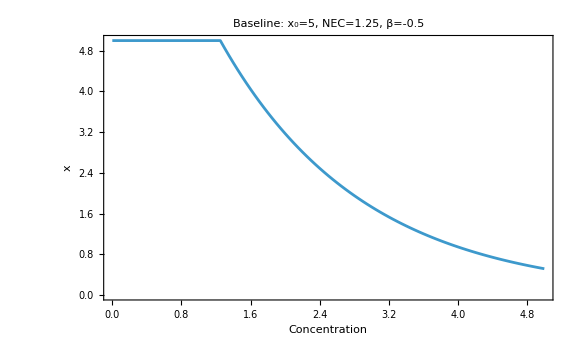

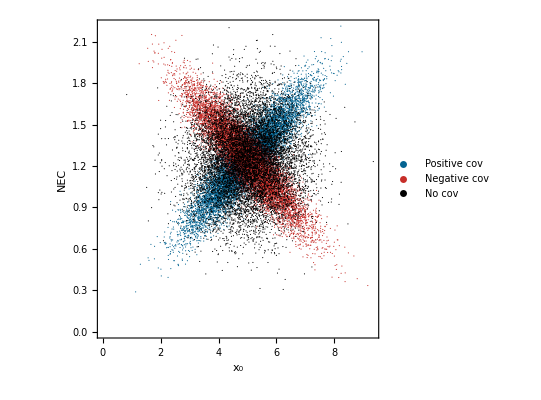

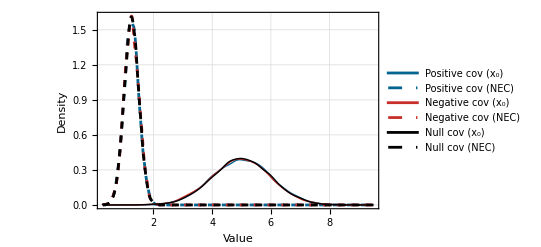

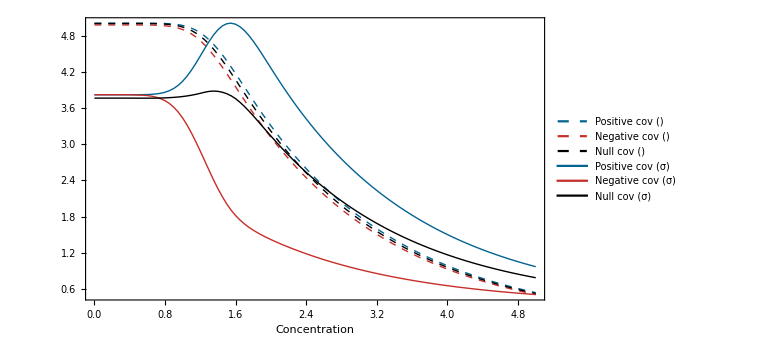

```mathematica
x0=5;
beta=-0.5;
Dose=Range[0,5,0.05];
NEC=1.25;
baseline=Table[
{d,DRFunLogExp[d,x0,beta,NEC]},
{d,Dose}
];
baselinePlot=plotBaseline[baseline];
nID=10000;
CVx=0.2;
CVnec=0.2;
SeedRandom[42];
rhoX0NEC=0.9;
individualsPos=GenerateIndividuals[x0,NEC,CVx,CVnec,rhoX0NEC,nID];
individualsNeg=GenerateIndividuals[x0,NEC,CVx,CVnec,-rhoX0NEC,nID];
individualsNull=GenerateIndividuals[x0,NEC,CVx,CVnec,0,nID];
{listPlot,histogram}=plotDistrib[individualsPos,individualsNeg,individualsNull,colPos,colNeg];
sigma=0.08;
(*Positive covariance between alpha and NEC*)
summaryPos=SimulateDoseResponse[individualsPos];
(*Negative covariance between alpha and NEC*)
summaryNeg=SimulateDoseResponse[individualsNeg];
(*No correlation between alpha and NEC*)
summaryNull=SimulateDoseResponse[individualsNull];
(*Concentration, mean Table for each population*)
meanPos=summaryPos[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
meanNeg=summaryNeg[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
meanNull=summaryNull[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
(*Concentration, standard deviation for each population*)
stdPos=summaryPos[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
stdNeg=summaryNeg[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
stdNull=summaryNull[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
fullPlot=plotResponse[meanPos,meanNeg,meanNull,stdPos,stdNeg,stdNull,0.2,colPos,colNeg];
baselinePlot
listPlot
histogram
fullPlot
```

#### Background plot

Let’s now load the data of stability, to create the background of the plot:

```mathematica
(* --- IMPORTING RESULTS --- *)
dataDir="D:\\OneDrive - agroparistech.fr\\predator-prey-ecotox-vi\\outputs\\data\\";
raw=Import[dataDir<>"fig_3_data.csv"];
dvals=ToExpression/@Rest[First[raw]];
σvals=ToExpression/@Rest[raw[[All,1]]];
data=ToExpression/@raw[[2;;,2;;]];

(* --- DEFINING PLOT --- *)
leg=SwatchLegend[
{Black,White,LightGray,Gray},
{"Noncoexistence","Coexistence: nonoscillatory","Coexistence: damped oscillations","Coexistence: limit cycles"},
LegendMarkers->"Rectangle"
];
backgroundPlot=Legended[
ArrayPlot[data,
DataReversed->True,
ColorRules->{
0->Black,
1->White,
2->LightGray,
3->Gray
},
Frame->True,
FrameTicks->{
Table[{i,Round[σvals[[i]],0.01]},{i,101,Length[dvals],100}],
Table[{i,Round[dvals[[i]],0.01]},{i,100,Length[σvals],100}]
},
FrameLabel->{"Phenotypic mismatch (d^2)","Individual variation (σ^2)"},
Mesh->False,
AspectRatio->1/1.5
],
leg
];
backgroundPlot
```

-Graphics-

#### Trajectories for varying dose

Let’s compute the stability for varying pesticide exposition:

```mathematica
sigmaPos=Table[std,{std,stdPos[[All,2]]}];
dvalsPos=Table[Abs[x0-mean],{mean,meanPos[[All,2]]}];
idMaxPos=Select[dvalsPos,#>2.5&->"Index"][[1]]-1;
coordsPos=Table[{sigmaPos[[i]],dvalsPos[[i]]},{i,Range[idMaxPos]}];
sigmaNeg=Table[std,{std,stdNeg[[All,2]]}];
dvalsNeg=Table[Abs[x0-mean],{mean,meanNeg[[All,2]]}];
idMaxNeg=Select[dvalsNeg,#>2.5&->"Index"][[1]]-1;
coordsNeg=Table[{sigmaNeg[[i]],dvalsNeg[[i]]},{i,Range[idMaxNeg]}];
sigmaNull=Table[std,{std,stdNull[[All,2]]}];
dvalsNull=Table[Abs[x0-mean],{mean,meanNull[[All,2]]}];
idMaxNull=Select[dvalsNull,#>2.5&->"Index"][[1]]-1;
coordsNull=Table[{sigmaNull[[i]],dvalsNull[[i]]},{i,Range[idMaxNull]}];
```

```mathematica
dIndex[d_]:=Rescale[d,{Min[dvals],Max[dvals]},{1,Length[dvals]}];
σIndex[s_]:=Rescale[s,{Min[σvals],Max[σvals]},{1,Length[σvals]}];
coordsPosPlot={dIndex[#1],σIndex[#2]}&@@@coordsPos;
coordsNegPlot={dIndex[#1],σIndex[#2]}&@@@coordsNeg;
coordsNullPlot={dIndex[#1],σIndex[#2]}&@@@coordsNull;
legFull={
SwatchLegend[
{Black,White,LightGray,Gray},
{"Noncoexistence","Coexistence: nonoscillatory","Coexistence: damped oscillations","Coexistence: limit cycles"},
LegendMarkers->"Rectangle"
],
LineLegend[
{colPos,colNeg,Green},
{"Positive cov","Negative cov","Null cov"}
]
};
fullPlot=Legended[
ArrayPlot[data,
DataReversed->True,
ColorRules->{
0->Black,
1->White,
2->LightGray,
3->Gray
},
Frame->True,
FrameTicks->{
Table[{i,Round[σvals[[i]],0.01]},{i,101,Length[dvals],100}],
Table[{i,Round[dvals[[i]],0.01]},{i,100,Length[σvals],100}]
},
FrameLabel->{"Phenotypic mismatch (d^2)","Individual variation (σ^2)"},
Mesh->False,
AspectRatio->1/1.5,
Epilog->{
{colPos,Thick,Line[coordsPosPlot]},
{colNeg,Thick,Line[coordsNegPlot]},
{Green,Thick,Line[coordsNullPlot]}
}
],
legFull
];
fullPlot
```

-Graphics-